# False Random Trend Lines

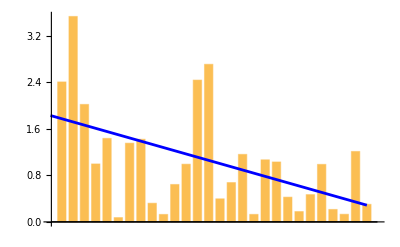
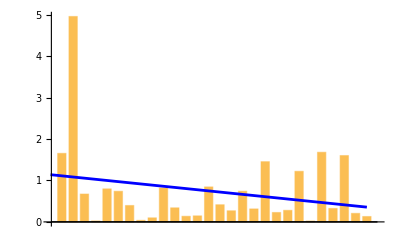
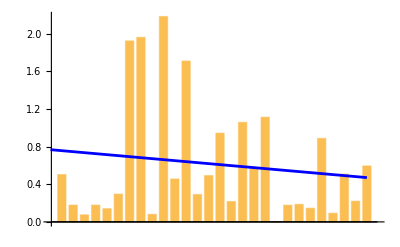
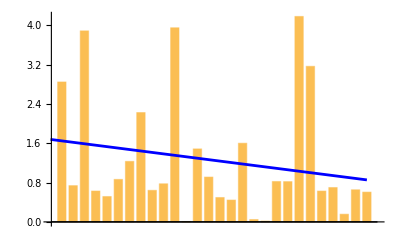
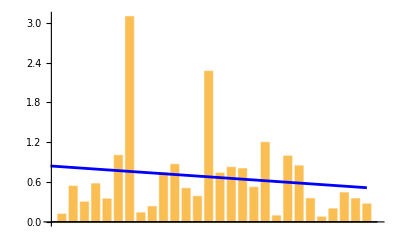
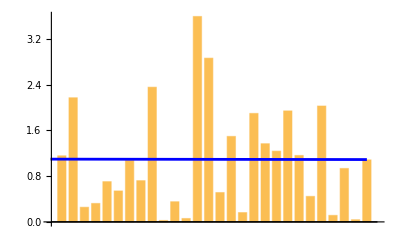
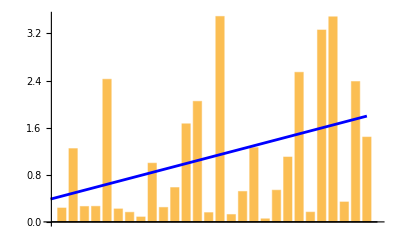
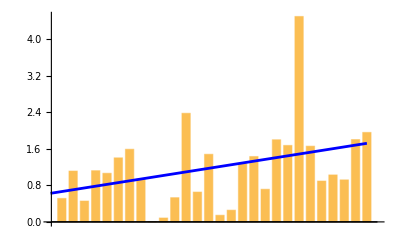

```mathematica
Table[data = RandomVariate[ExponentialDistribution[1],{28}];
lm = LinearModelFit[data,x,x];
Show[BarChart[data], Plot[lm[x],{x,0,28},PlotStyle->Blue,Frame->True]],{12}]
```